# Checking the absence of the inverted Marcus region in ET with quantum modes

## Units

Unit conversion factors:

```mathematica
bohr2a=0.529177`50;
a2bohr=1/bohr2a;
au2kcal=627.5095`50;
kcal2au=1/au2kcal;
ev2cm=8065.54477`50;
cm2ev = 1/ev2cm ;
au2ev=27.2113`50;
ev2au = 1/au2ev;
cm2au=cm2ev*ev2au;     
au2cm=1/cm2au;
ev2kcal=ev2au*au2kcal;
kcal2ev=1/ev2kcal;
au2ps=2.4189`50*10^(-5);
ps2au=1/au2ps;
au2fs=au2ps*1000;
fs2au=1/au2fs;
```

Physical constants:

```mathematica
hbar=1;
hbarps=0.047685388`50/(au2kcal*π);
Dalton=1822.8900409014022`50;
MassH=1.0072756064562605`50;
MassD=2.0135514936645316`50;
MassT=3.0160492`50;
mH=MassH*Dalton;
mD=MassD*Dalton;
mT=MassT*Dalton;
kb=3.16683`50*10^-6;
```

## Parameters of the two-state ET model

Electronic coupling (kcal/mol):

```mathematica
V=0.03`50*ev2kcal
```

0.6918186562200262390991977597542197542932531705578

Bath reorganization energy (kcal/mol) :

```mathematica
λ=20;
```

Mass of the quantum mode:

```mathematica
Mass=5;
```

Frequencies of the quantum mode for the reactant and product proton potentials (cm^-1):

```mathematica
f1=2000.0`50;
f2=2000.0`50;
```

Minima of the reactant and product potentials (Å→ Bohr):

```mathematica
xm1=0;
xm2=-0.5`50*a2bohr;
```

Harmonic potentials (kcal/mol):

```mathematica
U1[x_]:=au2kcal 1/2 Mass*Dalton*(f1*cm2au)^2(x-xm1)^2;
U2[x_]:=au2kcal 1/2 Mass*Dalton*(f2*cm2au)^2(x-xm2)^2;
```

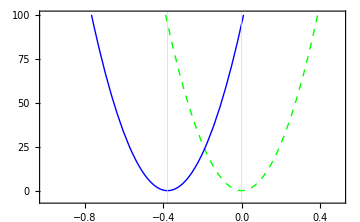

```mathematica
Plot[{U1[x],U2[x]},{x,-1,0.5},Axes->False,Frame->True,PlotStyle->{{Green,Dashed,AbsoluteThickness[1.0]},{Blue,AbsoluteThickness[1.0]},{Red,AbsoluteThickness[1.0]}},PlotRange->{-5,100},BaseStyle->{FontSize->14,FontFamily->"Helvetica"},FrameStyle->AbsoluteThickness[1.0],ImageSize->Medium,GridLines->{{xm1,xm2},None}]
```

Temperature (K):

```mathematica
T=30;
β=1/(kb*T);
```

## Harmonic oscillator energies and wavefunction overlaps

Harmonic energy levels (kcal/mol):

```mathematica
HarmEnergy[n_,f_]:=Module[{omega},
omega=f*cm2au;
au2kcal*omega*(n+1/2)];
```

Harmonic wavefunctions:

```mathematica
HarmWavefunction[n_,f_,x_,OptionsPattern[{M->MassH}]]:=Module[{mu,o,wnorm,w1,w2,q},
mu=OptionValue[M]*Dalton;
o=f*cm2au;
wnorm=((mu*o)/π)^(1/4)*2^(-n/2)*(n!)^(-1/2);
w1=Exp[-1/2 mu*o*x^2];
q=x*Sqrt[mu*o];
w2=HermiteH[n,q];
wnorm*w1*w2];
```

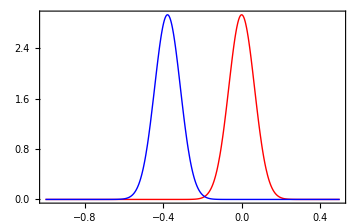

```mathematica
Plot[{HarmWavefunction[0,f1,x,M->Mass],HarmWavefunction[0,f2,x-xm2,M->Mass]},{x,-1,0.5},PlotRange->All,Axes->True,Frame->True,PlotStyle->{{Red,AbsoluteThickness[1.0]},{Blue,AbsoluteThickness[1.0]}},FrameStyle->AbsoluteThickness[1.0],BaseStyle->{FontSize->16,FontFamily->"Helvetica"},ImageSize->Medium]
```

Overlap integrals (in this expression the first oscillator is d Bohr to the right of the second one):

```mathematica
HarmOverlap[n1_,n2_,f1_,f2_,d_,OptionsPattern[{M->MassH,Acc->120}]]:=Module[{mass,acc,o1,o2,mu,a1,a2,s,A,Prefactor,b1,b2,i,j,Kaux},
acc=OptionValue[Acc];
mass=SetAccuracy[OptionValue[M],acc];
Kaux[i_,j_,a_,b_]:=SetAccuracy[If[OddQ[i+j],0,(i+j-1)!!/(a+b)^((i+j)/2)],acc];
mu=SetAccuracy[mass*Dalton,acc];
o1=SetAccuracy[f1*cm2au,acc];
o2=SetAccuracy[f2*cm2au,acc];
a1=SetAccuracy[(mu*o1),acc];
a2=SetAccuracy[(mu*o2),acc];
s=SetAccuracy[(a1*a2*d^2)/(a1+a2),acc];
A=SetAccuracy[(2*Sqrt[a1*a2])/(a1+a2),acc];
Prefactor=SetAccuracy[Sqrt[(A*Exp[-s])/(2^(n1+n2)*n1!*n2!)],acc];
b1=SetAccuracy[-((d*a2*Sqrt[a1])/(a1+a2)),acc];
b2=SetAccuracy[(d*a1*Sqrt[a2])/(a1+a2),acc];
Prefactor*Sum[Binomial[n1,i]*Binomial[n2,j]*HermiteH[n1-i,b1]*HermiteH[n2-j,b2]*(2*Sqrt[a1])^i*(2*Sqrt[a2])^j*Kaux[i,j,a1,a2],{j,0,n2},{i,0,n1}]];
```

```mathematica
Accuracy[HarmOverlap[10,21,f1,f2,xm1-xm2,M->Mass]]
```

93.236

## ET Rate constant

No Boltzmann distribution in the initial state: no thermal excitations

```mathematica
k[dG_,f1_,f2_,nmax_,T_,OptionsPattern[{M->MassH}]]:=Module[{mass,omega1,omega2,lambda},
mass=OptionValue[M];
omega1=f1*cm2au;
omega2=f2*cm2au;
lambda=λ*kcal2au;
10^12*ps2au*Sqrt[π/(lambda*kb*T)]*(V*kcal2au)^2*
Sum[
HarmOverlap[0,i,f1,f2,xm1-xm2,M->mass]^2*Exp[-(dG*kcal2au+lambda+(HarmEnergy[i,f2]-HarmEnergy[0,f1])*kcal2au)^2/(4*lambda*kb*T)]
,{i,0,nmax,1}]
];
```

```mathematica
HarmOverlap[0,30,f1,f2,xm1-xm2,M->Mass]
```

0.030680206265303399572716127251740034562599111095343637422158499413835667643398833061696813416304

## Free energy relationships

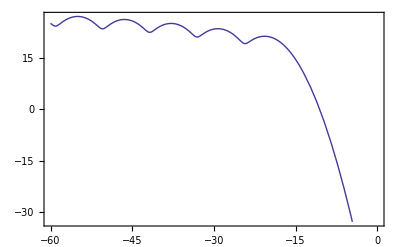

```mathematica
Plot[Log[k[x,2500,3000,30,30,M->1]],{x,-60,0},Axes->False,Frame->True]
```